```mathematica
<<SpinWeightedSpheroidalHarmonics`
<<KerrGeodesics`
<<GeneralRelativityTensor``
```

```mathematica
M=1;
a=.998;
r0 = 10;
ι = π/4;
```

```mathematica
Clear[Et,Qt,Lt]
```

```mathematica
Et[θ_]:=KerrGeoEnergy[a,r0,0,Cos[θ]]
Qt[θ_]:=KerrGeoCarterConstant[a,r0,0,Cos[θ]]
Lt[θ_]:=KerrGeoAngularMomentum[a,r0,0,Cos[θ]]
```

```mathematica
En[r_,L_]:=(a^2 L^2(r-M)+r (r^2-2M r +a^2)^2)/(a L M(r^2-a^2)+(r^2-2M r+a^2)√(r^5(r-3M)+a^4 r(r+M)+a^2 r^2(L^2-2M r+2 r^2)))
Q[r_,L_]:=(((a^2+r^2)En[r,L]-a L)^2)/(r^2-2M r +a^2)-(r^2+(L-a En[r,L])^2)
```

```mathematica
Lm = L/.Solve[ Q[r0,L]==L^2 Tan[ι]^2,L][[2,1]]
```

2.48413

```mathematica
Em = En[r0,Lm]
Qm = Q[r0,Lm]
```

0.952842

6.17092

```mathematica
Plot[{Lt[θ]-Lm},{θ,0,π/2},PlotLabels->{ "L"}]
```

-Graphics-

```mathematica
NSolve[Lt[θ]-Lm==0,{θ}]
```

$Aborted

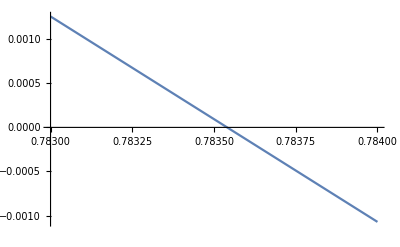

```mathematica
Plot[Lt[θ]-Lm,{θ,.783,.784}]
```

```mathematica
π/4//N
```

0.785398